# Fight back!

In this scenario, human starts fighting back to the zombies. 

This interactive tool numerically solves the dimensionless H–Z–R system, computes its Jacobian and stability indicators at the final state, and visualises the trajectories through time series, phase portraits, and trace–determinant plots.

```mathematica
Manipulate[
 Module[
  {
   eqns, sol, H, Z, R, t, Hfunc, Zfunc, Rfunc,
   phasePlotHZ, phasePlotZR, jMatrix,
   detJ, finalDetJ, traceJ, finalTraceJ,
   rFix, hFix
  },

  (* Dimensionless system consistent with screenshot *)
  eqns = {
    H'[t] == -(1 - R[t]) H[t] Z[t],
    Z'[t] == (1 - F) (1 - R[t]) H[t] Z[t],
    R'[t] == (c (1 - R[t]) - gamma) H[t]
  };

  (* Jacobian of the vector field f(H,Z,R) *)
  jMatrix = {
    {-(1 - R) Z,      -(1 - R) H,      H Z},
    {(1 - F)(1 - R) Z, (1 - F)(1 - R) H, -(1 - F) H Z},
    {c (1 - R) - gamma, 0, -c H}
  };

  (* Solve ODE numerically *)
  sol = NDSolve[
    {
     eqns,
     H[0] == H0,
     Z[0] == Z0,
     R[0] == R0
    },
    {H, Z, R},
    {t, 0, tmax},
    Method -> {"StiffnessSwitching"},
    MaxSteps -> Infinity
  ];

  Hfunc = H /. sol[[1]];
  Zfunc = Z /. sol[[1]];
  Rfunc = R /. sol[[1]];

  (* Numerical values at final time tmax for Jacobian *)
  hFix = Hfunc[tmax];
  rFix = Rfunc[tmax];

  traceJ = Tr[jMatrix];
  detJ = Det[jMatrix];

  finalTraceJ = traceJ /. {
     H -> (H[tmax] /. sol[[1]]),
     Z -> (Z[tmax] /. sol[[1]]),
     R -> (R[tmax] /. sol[[1]]),
     c -> c, gamma -> gamma, F -> F
  };

  finalDetJ = detJ /. {
     H -> (H[tmax] /. sol[[1]]),
     Z -> (Z[tmax] /. sol[[1]]),
     R -> (R[tmax] /. sol[[1]]),
     c -> c, gamma -> gamma, F -> F
  };

  (* H-Z subsystem for fixed R *)
  phasePlotHZ =
   StreamPlot[
    Evaluate[{
      -(1 - rFix) H Z,
      (1 - F)(1 - rFix) H Z
    }],
    {H, 0, hMaxPlot}, {Z, 0, zMaxPlot},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    Frame -> True,
    FrameLabel -> {"H", "Z"}
   ];

  (* Z-R subsystem for fixed H *)
  phasePlotZR =
   StreamPlot[
    Evaluate[{
      (1 - F)(1 - R) Z hFix,
      (c (1 - R) - gamma) hFix
    }],
    {Z, 0, zMaxPlot}, {R, 0, rMaxPlot},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    Frame -> True,
    FrameLabel -> {"Z", "R"}
   ];

  Column[{
    Plot[
     {Hfunc[t], Zfunc[t], Rfunc[t]},
     {t, 0, tmax},
     PlotRange -> All,
     PlotLegends -> {"H", "Z", "R"},
     PlotStyle -> {{Blue, Thick}, {Red, Thick}, {Purple, Thick}},
     Frame -> True,
     FrameLabel -> {"t", "H, Z, R"}
    ],

    phasePlotHZ,
    phasePlotZR,

    Show[
     ListPlot[
       {{finalDetJ, finalTraceJ}},
       PlotStyle -> Red,
       PlotRange -> {{-10, 10}, {-10, 10}},
       AxesLabel -> {"Determinant", "Trace"},
       PlotMarkers -> Automatic
     ],
     Frame -> True
    ]
   }]
 ],

 {{c, 1.0, "c"}, 0, 5, 0.01},
 {{gamma, 0.5, "gamma"}, 0, 5, 0.01},
 {{F, 0.2, "F"}, 0, 1, 0.01},

 Delimiter,
 {{H0, 1, "H0"}, 0, 10, 0.1},
 {{Z0, 0.2, "Z0"}, 0, 10, 0.1},
 {{R0, 0.5, "R0"}, 0, 1, 0.01},

 Delimiter,
 {{tmax, 50, "tmax"}, 1, 500, 1},

 Delimiter,
 {{hMaxPlot, 2, "H max"}, 0.1, 10, 0.1},
 {{zMaxPlot, 2, "Z max"}, 0.1, 10, 0.1},
 {{rMaxPlot, 1, "R max"}, 0.1, 2, 0.01}
]
```

## Eigenvalues Calculation

Defines the Jacobian and computes eigenvalues at each fixed-point family to determine stability.

```mathematica
(* Jacobian for the new model *)
jMatrix = {
  {-(1 - R) Z,          -(1 - R) H,        H Z},
  {(1 - F)(1 - R) Z,    (1 - F)(1 - R) H, -(1 - F) H Z},
  {c (1 - R) - gamma,    0,               -c H}
};

(* Fixed point families *)
fixedPointExtinction = {H -> 0};                       
fixedPointVictory    = {Z -> 0, R -> 1 - gamma/c};     

(* Eigenvalues *)
eigenExtinction = Eigenvalues[jMatrix /. fixedPointExtinction]
eigenVictory    = Eigenvalues[jMatrix /. fixedPointVictory]
```

{0,0,(-1+R) Z}

{0,-c H,-((-1+F) gamma H)/c}

## Bifurcation Analysis

A parameter sweep over  𝐹 is conducted by numerically solving the H–Z–R system for each value, extracting the asymptotic values of 𝐻 and 
𝑍, and plotting their dependence on 𝐹 to reveal the bifurcation structure.

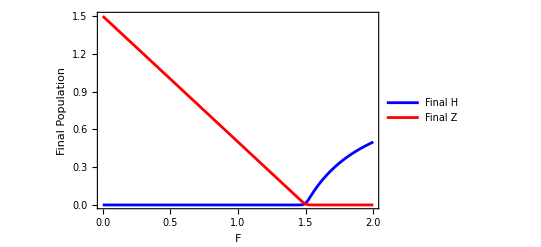

```mathematica
(* Bifurcation sweep in F for the new system *)

bifurcationData = Table[
  Module[
   {Fv, eqns, sol, Hf, Zf, Rf, Hfunc, Zfunc, Rfunc},
   Fv = Fval;   (* current F *)

   (* ODE system *)
   eqns = {
     H'[t] == -(1 - R[t]) H[t] Z[t],
     Z'[t] == (1 - Fv) (1 - R[t]) H[t] Z[t],
     R'[t] == (c*(1 - R[t]) - gamma) H[t]
   } /. {c -> 1.0, gamma -> 0.5};

   (* Solve ODEs *)
   sol = NDSolve[
     {
      eqns,
      H[0] == 1.0,
      Z[0] == 0.5,
      R[0] == 0.5
     },
     {H, Z, R},
     {t, 0, 300},
     Method -> {"StiffnessSwitching"},
     MaxSteps -> Infinity
   ];

   (* Extract solution functions *)
   Hfunc = H /. sol[[1]];
   Zfunc = Z /. sol[[1]];
   Rfunc = R /. sol[[1]];

   (* Final values *)
   Hf = Hfunc[300];
   Zf = Zfunc[300];
   Rf = Rfunc[300];

   {Fv, Hf, Zf, Rf}
  ],
  {Fval, 0, 2, 0.02}   (* F range *)
];

(* Unpack results *)
Fvals = bifurcationData[[All, 1]];
Hvals = bifurcationData[[All, 2]];
Zvals = bifurcationData[[All, 3]];
Rvals = bifurcationData[[All, 4]];

(* Plot bifurcation diagram *)
ListLinePlot[
 {
  Transpose[{Fvals, Hvals}],
  Transpose[{Fvals, Zvals}]
 },
 PlotLegends -> {"Final H", "Final Z"},
 PlotStyle -> {{Blue, Thick}, {Red, Thick}},
 Frame -> True,
 PlotRange -> All,
 FrameLabel -> {"F", "Final Population"}
]
```